```mathematica
(* Plotting package *)
<<MaTeX`
rasterListContourPlot[pList_,opts:OptionsPattern[]]:=Module[{img,cont,contL,plotRangeRule,contourOptions,frameOptions,rangeCoords},contourOptions=Join[FilterRules[{opts},FilterRules[Options[ListContourPlot],Except[{Background,Frame,Axes}]]],{Frame->None,Axes->None}];
contL=ListContourPlot[pList,Evaluate@Apply[Sequence,contourOptions]];
cont=First[Cases[{contL},Graphics[__],Infinity]];
img=Rasterize[Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,1]]],PlotRangePadding->None,ImagePadding->None,Options[cont,PlotRange]],"Image",ImageSize->With[{size=Total[{2,0} (ImageSize/.{opts})/.{ImageSize->CurrentValue[ImageSize]}]},If[NumericQ[size],size,First[WindowSize/.Options[EvaluationNotebook[]]]]]];
plotRangeRule=FilterRules[AbsoluteOptions[cont],PlotRange];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
If[Head[contL]===Legended,Legended[#,contL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,2]]]],Evaluate@Apply[Sequence,frameOptions]]]
(* These functions can basically be ignored. It's just dealing with the graphics for when I want to format my publication-quality plots. *)
Clear[undistortedGraphicsColumn];
Options[undistortedGraphicsColumn]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsColumn[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,width, xsizes, ysizes},width=Max@sizes[[All,1]];
ysizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@list-1]];
xsizes = sizes[[All, 1]];
Graphics[Table[Inset[list[[i]],{(width - xsizes[[i]]) / 2,-Plus@@ysizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{width,Plus@@ysizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@ysizes,0}},AspectRatio->Plus@@ysizes/width,PlotRangePadding->None]]

Clear[undistortedGraphicsRow];
Options[undistortedGraphicsRow]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsRow[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,height, xsizes, ysizes},height=Max@sizes[[All,2]];
xsizes=sizes[[All,1]]+Join[ConstantArray[OptionValue[Spacings],Length@list-1],{0}];
ysizes = sizes[[All, 2]];
Graphics[Table[Inset[list[[i]],{If[i>1, Plus@@xsizes[[;;i-1]],0], (height-ysizes[[i]])/2},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{Plus@@xsizes, height},ImagePadding->None,PlotRange->{{0, Plus@@xsizes}, {0, height}},AspectRatio->height/(Plus@@xsizes),PlotRangePadding->None]]

Clear[format]
Options[format] = Options[PaddedForm];
format[x_, sd_]:=Module[{m,e},
{m,e} = MantissaExponent[x];
If[x == 0, "0",If[-2≤e≤2,ToString[PaddedForm[x, sd]],ToString[PaddedForm[ToExpression[ToString[m]]*10, sd]]<>"\\times10^{"<>ToString[e-1]<>"}"]]
]
```

```mathematica
(*
(*This part is for calculating the efficiency of the lower bound*)
f = Compile[{{x, _Real}, {y, _Real},{k1, _Real},{k2, _Real},{k3, _Real},{gamma, _Real} },{-(k1+k2)/gamma*x+k2/gamma*y,k2/gamma*x-(k2+k3)/gamma*y}];
AllNeighbors = Compile[{{i, _Integer}, {sqrtlenfpoints, _Integer}},
(* First handle the four corners *)
If[i==1, {2, sqrtlenfpoints+1},
If[i==sqrtlenfpoints, {sqrtlenfpoints - 1, 2 sqrtlenfpoints},
If[i==sqrtlenfpoints^2-sqrtlenfpoints+1, {sqrtlenfpoints^2-2sqrtlenfpoints+1, sqrtlenfpoints^2-sqrtlenfpoints+2},
If[i==sqrtlenfpoints^2, {sqrtlenfpoints^2-1, sqrtlenfpoints^2-sqrtlenfpoints},
(* Then handle the top and bottom boundary *)
If[1<i<sqrtlenfpoints, {i-1, i+1, i+sqrtlenfpoints},
If[sqrtlenfpoints^2-sqrtlenfpoints+1<i<sqrtlenfpoints^2,{i-1, i+1, i-sqrtlenfpoints},
(* Then handle the left and right boundary *)
If[Mod[i,sqrtlenfpoints]==1, {i-sqrtlenfpoints, i+1, i+sqrtlenfpoints},
If[Mod[i, sqrtlenfpoints]==0, {i-sqrtlenfpoints, i-1, i+sqrtlenfpoints},
(* Otherwise you have four neighbors *)
{i-sqrtlenfpoints, i-1, i+1, i+sqrtlenfpoints}
]
]
]
]
]
]
]
]
];
Wright = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real},{k1, _Real},{k2, _Real},{k3, _Real},{gamma, _Real}},(f[x,y,k1,k2,k3,gamma][[1]] / (2h)) + (Diffusion / h^2)];
Wleft = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real},{k1, _Real},{k2, _Real},{k3, _Real},{gamma, _Real}},-(f[x,y,k1,k2,k3,gamma] [[1]]/ (2h)) + (Diffusion / h^2)];
Wup = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real},{k1, _Real},{k2, _Real},{k3, _Real},{gamma, _Real}},(f[x,y,k1,k2,k3,gamma] [[2]]/ (2h)) + (Diffusion / h^2)];
Wdown = Compile[{{x, _Real}, {y, _Real}, {h, _Real}, {Diffusion, _Real},{k1, _Real},{k2, _Real},{k3, _Real},{gamma, _Real}},-(f[x,y,k1,k2,k3,gamma] [[2]]/ (2h)) + (Diffusion / h^2)];

T2=50;
k2=1;
gamma=1;
kb=1;
Binnum=100;
(*k1=2;*)

effic=Table[
(*Table[*)

T1=(1/tempratio)*T2;
spriratio=k1/k2;
k3=k1;
Diffusion={kb*T1/gamma,kb*T2/gamma};
spacescale=Sqrt[2kb*gamma*T1/k2];
xmax=100/(10 √10)*spacescale;
ymax=40/(10 √10)*spacescale;
xmin = -xmax;
ymin = -ymax;
h = {2*xmax,2*ymax}/(Binnum-1);
points = N[Table[{x, y}, {x, xmin, xmax, h[[1]]}, {y, ymin, ymax, h[[2]]}]];
fpoints = Round[Flatten[points, 1],h[[2]]/400000];
edges =Flatten[Table[{i, j}, {i,1,Length[fpoints]}, {j, AllNeighbors[i, Sqrt[Length[fpoints]]]}],1];

W = SparseArray[
Table[
{i,j}=edge;
point1 = fpoints[[j]];
point2 = fpoints[[i]];
posdiff=point1-point2;
{i,j}->If[posdiff[[2]]>0,Wdown[point1[[1]], point1[[2]], h[[2]], Diffusion[[2]], k1,k2,k3,gamma], 
If[posdiff[[2]]<0,Wup[point1[[1]], point1[[2]], h[[2]], Diffusion[[2]], k1,k2,k3,gamma],
If[posdiff[[1]]>0, Wleft[point1[[1]], point1[[2]], h[[1]], Diffusion[[1]], k1,k2,k3,gamma],
Wright[point1[[1]], point1[[2]], h[[1]], Diffusion[[1]],k1,k2,k3,gamma]
]
]
],
{edge, edges}
]
];

tot = Total[W, {1}];
Wdiag = Table[
{i, i}->tot[[i]],
{i, 1,Length[fpoints]}
];
W -=SparseArray[Wdiag];

evseed = Eigenvectors[W, 1, Method->{"Arnoldi", "Criteria"->"RealPart", "MaxIterations"->250000}][[1]];
ev = evseed;
lev = Table[1, {i, 1, Length[W]}];
lev = lev *Length[lev]/ Total[lev];
ev = Re[evseed / (lev.evseed)];

thermodynamicforces = SparseArray[
Reap[
Do[
{i, j} = edge;Sow[{j,i}->Log[(W[[i,j]]ev[[j]])/(ev[[i]]W[[j,i]])]];,{edge, edges}
]
][[2,1]]
];

currents = SparseArray[
Reap[
Do[
{i,j} = edge;Sow[{j,i}->(W[[i,j]]ev[[j]])-(ev[[i]]W[[j,i]])];,{edge,edges}
]
][[2,1]]
];

Σnum=Chop[Total[Total[thermodynamicforces*currents]]]/2;
Clear[z];
Wtilt = W * Exp[z thermodynamicforces];
eigenvec = {evseed};
ψ=Table[
z = zv;
{eigenval, eigenvec} = 
Chop[
Eigensystem[Wtilt,
1,
Method->{"Arnoldi", "Criteria"->"RealPart", "StartingVector"->evseed,"MaxIterations"->250000}
]
];
{z, First[eigenval]},
{zv, 0.001, 0.002, 0.001}
];
minxval = -ψ[[1,2]] / ψ[[1, 1]];
varval = 4(ψ[[2, 2]] - (ψ[[1,2]] / ψ[[1, 1]])*ψ[[2, 1]]) / (ψ[[2, 1]]^2);

Σthermo= 2 * (minxval)^2/varval;
Σana=N[(k2^2*(T1-T2)^2)/(2*(k1+k2)*T1*T2)];
η=Σthermo/Σana;

Print["Computed Lower Bound Efficiency "<>ToString[η]<>"."];
Print["Calculating the k1 "<>ToString[k1]<>"."];
{tempratio,spriratio,η}
,{tempratio,0.05,0.95,0.05}]
,{k1,0.1,2.1,0.02}];
(*Export["/Users/junangli/Desktop/effec.mat",effic];*)
```

```mathematica
effic=Import[NotebookDirectory[]<>"../../data/effec.mat"];
(*
effic=Import["/Users/junangli/Desktop/effec.mat"];
effic[[1,1,3]]=effic[[1,5,3]];
effic[[1,2,3]]=effic[[1,5,3]];
effic[[1,3,3]]=effic[[1,5,3]];
effic[[1,4,3]]=effic[[1,5,3]];
effic[[2,1,3]]=effic[[1,5,3]];
*)
```

```mathematica
cmap = Blend[{RGBColor[{0, 0, 255}/255], RGBColor[{255, 0, 0}/255]}, #]&;
minv = 0;
maxv = 1;
(*maxv=0.004;*)


ticklocations = N[FindDivisions[{minv, maxv}, 5]];

minv = ticklocations[[1]];
maxv = ticklocations[[-1]];
stepv = (maxv - minv) /10.;
cmap2 = cmap[(#-minv) / (10.*stepv)]&;

ymin=0;
ymax=2;
xmin=0;
xmax=1;
xmajor=0.1;
xminor=0.05;
ymajor=0.2;
yminor=0.1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
EfficientPlot = Show[
rasterListContourPlot[Flatten[effic,1],
ColorFunction->cmap2,
PlotRange->Full,
ColorFunctionScaling->False
],

Frame->True,
FrameTicks->ft,
FrameLabel->{MaTeX["\\textrm{Temperature ratio} \\quad {T_{\\rm c} }/{T_{\\rm h}}",FontSize->20](*,MaTeX["\\text{Spring constant ratio} \\quad {k_1}/{k_2}",FontSize->20]*)},
ImageSize->400,
AspectRatio->1,
ImagePadding->{{85,10},{85,30}}
]
```

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

-Graphics-

```mathematica
cmap = Blend[{RGBColor[{0, 0, 255}/255], RGBColor[{255, 0, 0}/255]}, #]&;
minv = 0;
maxv =1;

ticklocations = N[FindDivisions[{minv, maxv}, 5]];

minv = ticklocations[[1]];
maxv = ticklocations[[-1]];
stepv = (maxv - minv) /10.;
cmap2 = cmap[(#-minv) / (10.*stepv)]&;

ticklabels=MaTeX[format[#,{2,1}], FontSize->14]&/@ticklocations;
Efficientcolorbar = Graphics[
Table[Inset[ticklabels[[i]],Scaled[{0.65, ((0.873-0.10)/(Length[ticklocations]-1))(i-1) + 0.10}]], {i, 1, Length[ticklocations]}],
ImageSize->{110, 350},
Epilog->Inset[
BarLegend[{cmap2, {minv, maxv}},
LegendMarkerSize->{30, 310},
"Ticks"->ticklocations,
"TickLabels"->(""&/@ticklocations),
Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}]/.AbsoluteThickness[_]->AbsoluteThickness[2],
Scaled[{0, 0}], Scaled[{0, 0}]
],
Prolog->Text[MaTeX["\\eta", FontSize->18],Scaled[{0.23, 0.94}]],
AspectRatio->Full
]
```

-Graphics-

```mathematica
Efficientcolorbar=undistortedGraphicsColumn[{ Efficientcolorbar, Graphics[{}, ImageSize->{110, 40}]}]
```

-Graphics-

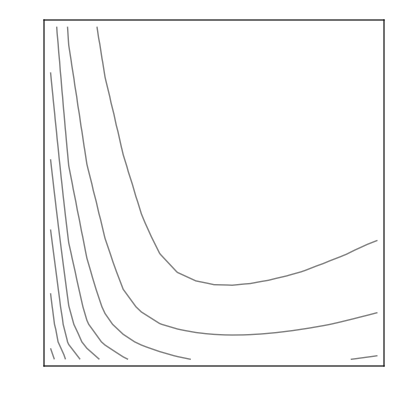

```mathematica
patch2=undistortedGraphicsRow[{EfficientPlot, Efficientcolorbar}]
```

```mathematica
T2=50;
k2=1;
Dissipationrate=Table[
Table[
T1=T2/tempratio;
{tempratio,k1/k2,(k2^2*(T1-T2)^2)/(2*(k1+k2)*T1*T2)}
,{tempratio,0.1,0.95,0.005}]
,{k1,0.1,2,0.01}];
```

```mathematica
cmapdensity = ColorData["M10DefaultDensityGradient"];
mind= Round[Min[Transpose[Flatten[Dissipationrate,1]][[-1]]]];
maxd = Round[Max[Transpose[Flatten[Dissipationrate,1]][[-1]]]];

ticklocationsd = N[FindDivisions[{mind, maxd}, 10]];

mind = ticklocationsd[[1]];
maxd = ticklocationsd[[-1]];
stepd = (maxd - mind) /50.;
cmapdensity2 = cmapdensity[(#-mind) / (50.*stepd)]&;
ymin=0;
ymax=2;
xmin=0;
xmax=1;
xmajor=0.1;
xminor=0.05;
ymajor=0.2;
yminor=0.1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
DissipationratePlot = Show[
rasterListContourPlot[Flatten[Dissipationrate,1],
ColorFunction->cmapdensity2,
PlotRange->Full,
ColorFunctionScaling->False
],

Frame->True,
FrameTicks->ft,
FrameLabel->{MaTeX["\\textrm{Temperature ratio} \\quad {T_{\\rm c} }/{T_{\\rm h}}",FontSize->20],MaTeX["\\text{Spring constant ratio} \\quad {k_1}/{k_2}",FontSize->20]},
ImageSize->400,
AspectRatio->1,
ImagePadding->{{85,10},{85,30}}]
```

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

-Graphics-

```mathematica
cmap4 = ColorData["M10DefaultDensityGradient"];
ticklocations = Round[FindDivisions[{mind, maxd}, 5]];

mind = ticklocations[[1]];
maxd = ticklocations[[-1]];
stepd = (maxd - mind) /10.;
cmap3= cmap4[(#-mind) / (10*stepd)]&;

ticklabels=MaTeX[format[#,{2,1}], FontSize->14]&/@ticklocations;
Dissipationratecolorbar = Graphics[
Table[Inset[ticklabels[[i]],Scaled[{0.65, ((0.873-0.10)/(Length[ticklocations]-1))(i-1) + 0.10}]], {i, 1, Length[ticklocations]}],
ImageSize->{110, 350},
Epilog->Inset[
BarLegend[{cmap3, {mind, maxd}},
LegendMarkerSize->{30, 310},
"Ticks"->ticklocations,
"TickLabels"->(""&/@ticklocations),
Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}]/.AbsoluteThickness[_]->AbsoluteThickness[2],
Scaled[{0, 0}], Scaled[{0, 0}]
],
Prolog->Text[MaTeX["\\dot S_{\\rm ss}", FontSize->18],Scaled[{0.24, 0.94}]],
AspectRatio->Full
]
```

-Graphics-

```mathematica
Dissipationratecolorbar=undistortedGraphicsColumn[{ Dissipationratecolorbar, Graphics[{}, ImageSize->{110, 40}]}]
```

-Graphics-

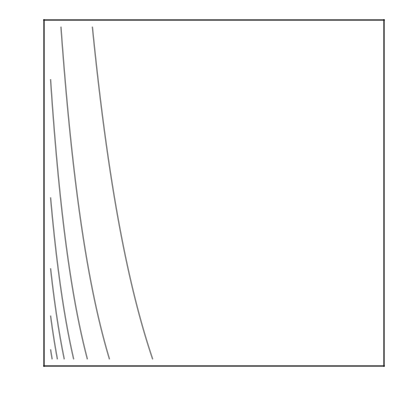

```mathematica
patch1=undistortedGraphicsRow[{DissipationratePlot, Dissipationratecolorbar}]
```

```mathematica
SIfig2=
Show[
undistortedGraphicsRow[{patch1,patch2},Spacings-> -60],
Prolog-> {Inset[Text[MaTeX["\\text{(a)}", FontSize->24]], Scaled[{0.045, 0.96}]],
Inset[Text[MaTeX["\\text{(b)}", FontSize->24]], Scaled[{0.515, 0.96}]]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"SIfig2.pdf", SIfig2];
Export[NotebookDirectory[]<>"../SIfig2.pdf", SIfig2];
```